## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW150914";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_0","dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_6l","dphi_7"};
intermediateParams={"dbeta_2","dbeta_3"};
mergerParams={"dalpha_2","dalpha_3","dalpha_4"};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

```mathematica
raw=Import[FileNameJoin[{baseDir,eventID,"GR"<>"_IMRP_posterior.csv"}]];
samples["GR"]=(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]](*spin2z*)};
```

```mathematica
Quantile[samples["GR"][[1]],{0.05,0.50,0.95}]
Quantile[samples["GR"][[2]],{0.05,0.50,0.95}]
Quantile[samples["GR"][[2]],{0.05,0.50,0.95}]
```

{32.4086,35.2935,40.2245}

{25.9935,30.3388,33.2104}

{25.9935,30.3388,33.2104}

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

```mathematica
samples["dalpha_3"][[6]]
```

```mathematica
CalculateSampleRatios[samples,{35.5,29.9},{35.5-3.1,29.9-4.5},{35.5+5.1,29.9+3.0}]
```

{<|p→dphi_0,LowerBoundRatios→<|1→1.05627,2→0.841538|>,MedianRatios→<|1→1.0885,2→0.994134|>,UpperBoundRatios→<|1→1.09104,2→1.06441|>,WidthRatios→<|1→1.22842,2→1.81918|>|>,<|p→dphi_2,LowerBoundRatios→<|1→1.04185,2→0.827033|>,MedianRatios→<|1→1.09698,2→0.958047|>,UpperBoundRatios→<|1→1.09844,2→1.04686|>,WidthRatios→<|1→1.32205,2→1.79133|>|>,<|p→dphi_3,LowerBoundRatios→<|1→1.03444,2→0.844279|>,MedianRatios→<|1→1.07575,2→0.982997|>,UpperBoundRatios→<|1→1.08597,2→1.04639|>,WidthRatios→<|1→1.28956,2→1.73087|>|>,<|p→dphi_4,LowerBoundRatios→<|1→1.04008,2→0.822671|>,MedianRatios→<|1→1.10338,2→0.951138|>,UpperBoundRatios→<|1→1.10638,2→1.04022|>,WidthRatios→<|1→1.36831,2→1.77698|>|>,<|p→dphi_5l,LowerBoundRatios→<|1→1.04654,2→0.846059|>,MedianRatios→<|1→1.09595,2→0.96028|>,UpperBoundRatios→<|1→1.0979,2→1.035|>,WidthRatios→<|1→1.30082,2→1.6749|>|>,<|p→dphi_6,LowerBoundRatios→<|1→1.04267,2→0.901142|>,MedianRatios→<|1→1.07958,2→0.987286|>,UpperBoundRatios→<|1→1.08485,2→1.04476|>,WidthRatios→<|1→1.25151,2→1.53115|>|>,<|p→dphi_6l,LowerBoundRatios→<|1→1.03872,2→0.868742|>,MedianRatios→<|1→1.08513,2→0.977471|>,UpperBoundRatios→<|1→1.07935,2→1.04093|>,WidthRatios→<|1→1.23988,2→1.62406|>|>,<|p→dphi_7,LowerBoundRatios→<|1→1.04554,2→0.918951|>,MedianRatios→<|1→1.075,2→0.993093|>,UpperBoundRatios→<|1→1.08226,2→1.04587|>,WidthRatios→<|1→1.22736,2→1.47568|>|>,<|p→dbeta_2,LowerBoundRatios→<|1→1.05685,2→1.07254|>,MedianRatios→<|1→1.0812,2→1.08786|>,UpperBoundRatios→<|1→1.09388,2→1.10174|>,WidthRatios→<|1→1.24023,2→1.20062|>|>,<|p→dbeta_3,LowerBoundRatios→<|1→1.07938,2→1.12354|>,MedianRatios→<|1→1.08037,2→1.10386|>,UpperBoundRatios→<|1→1.09234,2→1.09511|>,WidthRatios→<|1→1.14353,2→0.998824|>|>,<|p→dalpha_2,LowerBoundRatios→<|1→1.07955,2→1.11261|>,MedianRatios→<|1→1.09623,2→1.11124|>,UpperBoundRatios→<|1→1.10693,2→1.12654|>,WidthRatios→<|1→1.21513,2→1.17373|>|>,<|p→dalpha_3,LowerBoundRatios→<|1→1.08645,2→1.10113|>,MedianRatios→<|1→1.09462,2→1.09464|>,UpperBoundRatios→<|1→1.09458,2→1.10867|>,WidthRatios→<|1→1.12669,2→1.13419|>|>,<|p→dalpha_4,LowerBoundRatios→<|1→1.08955,2→1.12267|>,MedianRatios→<|1→1.087,2→1.10553|>,UpperBoundRatios→<|1→1.0803,2→1.10872|>,WidthRatios→<|1→1.04375,2→1.06148|>|>}

## m1-m2 Plot, 22

```mathematica
plots=<||>;
compPlots=<||>;
vsPlots=<||>;
vsPlots["p2p4"]={};
```

## INSPIRAL

### phi_2 v.s. phi_4

```mathematica
p="GR"
m1Data=samples["GR"][[1]];
m2Data=samples["GR"][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.001643};
contourPD[p]={0.0014553};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

GR

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 40836 + 镜像 40836

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.7701×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.7701×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.0014553}，共 2 条

第一条前3点：{{30.0512,30.7152},{30.0274,30.7409},{29.8688,30.8728}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.930928

可信水平百分比：93.0928%

==========================

GR 预处理完成，红线包含概率 prob = 0.930928

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.0351227, 0.964877}

实际使用的 GR 概率区间上下界: {6.23755, 6.44165}

实际使用的 Param 概率区间上下界: {1.93366, 6.40303}

GR下界: 点数=500 | Y>0点数=500 | 平均误差=1.32339×10^-15

GR上界: 点数=500 | Y>0点数=500 | 平均误差=3.73035×10^-16

Param下界: 点数=500 | Y>0点数=500 | 平均误差=2.98039

Param上界: 点数=500 | Y>0点数=500 | 平均误差=7.15872×10^-16

{{10.1,2.0709×10^6},{10.2,2.09141×10^6},{10.3,2.11191×10^6},{10.4,2.13242×10^6},{10.5,2.15293×10^6}}

{{10.1,7.32439},{10.2,7.39691},{10.3,7.46943},{10.4,7.54195},{10.5,7.61447}}

chi1L取值：0.258801

chi2L取值：0.347617

=====================================================

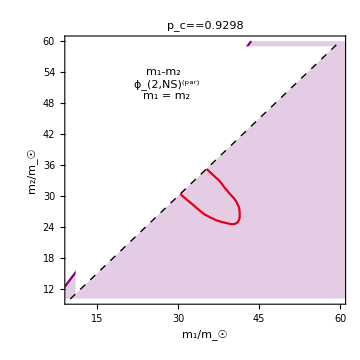

```mathematica
probability=prob;

temp=PlotInversion["dphi_2",probability,10,60,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

```mathematica
AppendTo[vsPlots["p2p4"],temp];
```

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.0345, 0.9655}

实际使用的 GR 概率区间上下界: {43.6686, 46.2435}

实际使用的 Param 概率区间上下界: {-121.589, 45.2369}

GR下界: 点数=500 | Y>0点数=500 | 平均误差=8.3844×10^-16

GR上界: 点数=500 | Y>0点数=500 | 平均误差=1.08429×10^-14

Param下界: 点数=500 | Y>0点数=500 | 平均误差=151.693

Param上界: 点数=500 | Y>0点数=500 | 平均误差=7.10543×10^-15

{{10.1,358580.},{10.2,362131.},{10.3,365682.},{10.4,369231.},{10.5,372782.}}

{{10.1,16.2168},{10.2,16.3774},{10.3,16.538},{10.4,16.6985},{10.5,16.8591}}

chi1L取值：0.262031

chi2L取值：0.383743

=====================================================

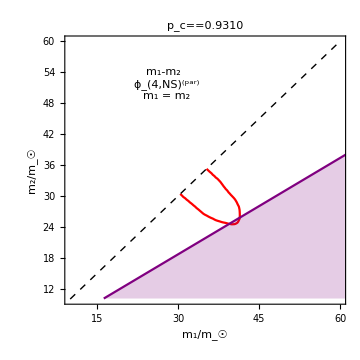

```mathematica
probability=prob;
probability=0.9310;

temp=PlotInversion["dphi_4",probability,10,60,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

```mathematica
AppendTo[vsPlots["p2p4"],temp];
```

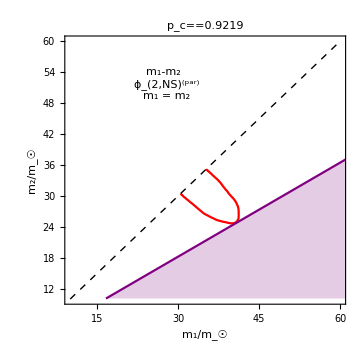
{-Graphics-,-Graphics-}

```mathematica
vsPlots["p2p4"]
```

### phi_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.001203};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 17687 + 镜像 17687

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.86295×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.86295×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.001203}，共 2 条

第一条前3点：{{28.7408,28.0768},{28.7845,28.0298},{28.8632,27.908}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.893956

可信水平百分比：89.3956%

==========================

dphi_2 预处理完成，红线包含概率 prob = 0.893956

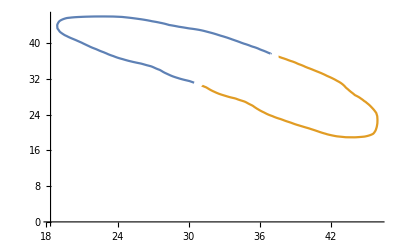

```mathematica
ListLinePlot[contourPoints[p]]
```

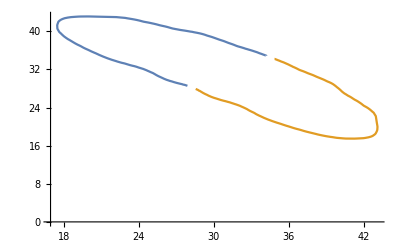

```mathematica
ListLinePlot[contourPoints[p]]
```

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.0530222, 0.946978}

实际使用的 GR 概率区间上下界: {6.25916, 6.44146}

实际使用的 Param 概率区间上下界: {2.18177, 6.19599}

GR下界: 点数=500 | Y>0点数=500 | 平均误差=2.20268×10^-16

GR上界: 点数=500 | Y>0点数=500 | 平均误差=5.3646×10^-16

Param下界: 点数=500 | Y>0点数=500 | 平均误差=2.73227

Param上界: 点数=500 | Y>0点数=500 | 平均误差=8.72191×10^-16

{{10.1,2.25897×10^6},{10.2,2.28134×10^6},{10.3,2.30371×10^6},{10.4,2.32607×10^6},{10.5,2.34844×10^6}}

{{10.1,23.6294},{10.2,23.8633},{10.3,24.0973},{10.4,24.3312},{10.5,24.5652}}

chi1L取值：0.258801

chi2L取值：0.347617

=====================================================

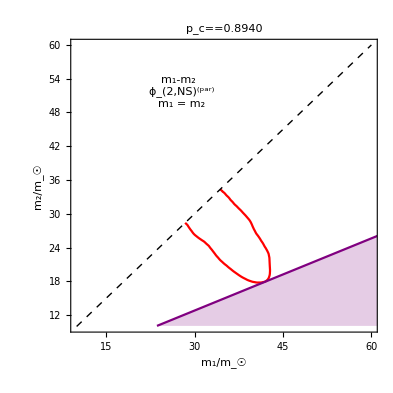

```mathematica
probability=prob;
(*probability=0.8925058374665041;
probability=0.9;*)
(*probability=0.89;*)

plots[p]=PlotInversion[p,probability,10,60,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### phi_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.000879};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 16389 + 镜像 16389

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.20691×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.20691×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.000879}，共 2 条

第一条前3点：{{28.1169,27.4536},{28.1171,27.4531},{28.2538,27.3619}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.923711

可信水平百分比：92.3711%

==========================

dphi_4 预处理完成，红线包含概率 prob = 0.923711

```mathematica
p="dphi_4"; 
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
prob
```

0.923761

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.0381447, 0.961855}

实际使用的 GR 概率区间上下界: {43.7431, 46.2429}

实际使用的 Param 概率区间上下界: {-119.654, 42.9149}

GR下界: 点数=450 | Y>0点数=450 | 平均误差=3.06323×10^-15

GR上界: 点数=450 | Y>0点数=450 | 平均误差=3.8843×10^-15

Param下界: 点数=450 | Y>0点数=450 | 平均误差=149.759

Param上界: 点数=450 | Y>0点数=450 | 平均误差=8.88968×10^-15

{{10.1,363213.},{10.2,366810.},{10.3,370405.},{10.4,374001.},{10.5,377596.}}

{{10.1,25.1066},{10.2,25.3552},{10.3,25.6038},{10.4,25.8524},{10.5,26.1009}}

chi1L取值：0.262031

chi2L取值：0.383743

=====================================================

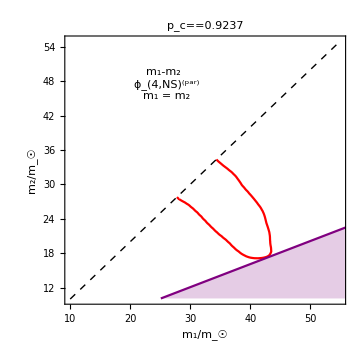

```mathematica
probability=prob;
(*probability=0.9237609941746582;*)
(*probability=0.535;*)
(*probability=0.91;*)

plots[p]=PlotInversion[p,probability,10,55,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### phi_5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_5l"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0006072};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 16958 + 镜像 16958

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.20934×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.20933×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.0006072}，共 2 条

第一条前3点：{{27.6719,28.3358},{27.5638,28.4305},{27.2804,28.621}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.953992

可信水平百分比：95.3992%

==========================

dphi_5l 预处理完成，红线包含概率 prob = 0.953992

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.02295, 0.97705}

实际使用的 GR 概率区间上下界: {464.757, 467.038}

实际使用的 Param 概率区间上下界: {467.416, 1097.35}

GR下界: 点数=250 | Y>0点数=250 | 平均误差=3.18323×10^-15

GR上界: 点数=250 | Y>0点数=250 | 平均误差=3.81988×10^-14

Param下界: 点数=250 | Y>0点数=250 | 平均误差=5.68434×10^-14

Param上界: 点数=250 | Y>0点数=250 | 平均误差=615.586

{{10.2,23.5367},{10.4,23.9982},{10.6,24.4597},{10.8,24.9212},{11.,25.3827}}

{{10.2,112745.},{10.4,114956.},{10.6,117167.},{10.8,119377.},{11.,121588.}}

chi1L取值：0.28772

chi2L取值：0.362064

=====================================================

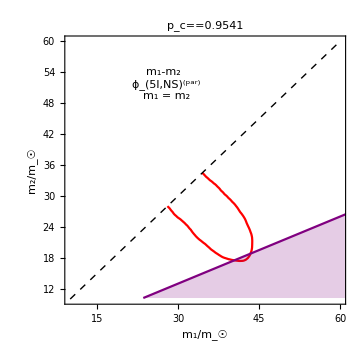

```mathematica
probability=prob;
(*probability=0.9543;*)
probability=0.9541;

plots[p]=PlotInversion[p,probability,10,60,0.2,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiLNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_6"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00109};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 18998 + 镜像 18998

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.8108×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.8108×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.00109}，共 2 条

第一条前3点：{{34.742,33.7403},{34.8201,33.6671},{35.0794,33.4658}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.922341

可信水平百分比：92.2341%

==========================

dphi_6 预处理完成，红线包含概率 prob = 0.922341

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.0388296, 0.96117}

实际使用的 GR 概率区间上下界: {-1104.05, -1021.21}

实际使用的 Param 概率区间上下界: {-998.827, 1396.8}

GR下界: 点数=500 | Y>0点数=500 | 平均误差=1.30967×10^-13

GR上界: 点数=500 | Y>0点数=500 | 平均误差=1.04137×10^-13

Param下界: 点数=500 | Y>0点数=500 | 平均误差=1.50521×10^-13

Param上界: 点数=500 | Y>0点数=500 | 平均误差=1675.07

{{10.1,21.3173},{10.2,21.5283},{10.3,21.7394},{10.4,21.9505},{10.5,22.1615}}

{{10.1,1.99475×10^6},{10.2,2.0145×10^6},{10.3,2.03425×10^6},{10.4,2.054×10^6},{10.5,2.07375×10^6}}

chi1L取值：0.233562

chi2L取值：0.324994

=====================================================

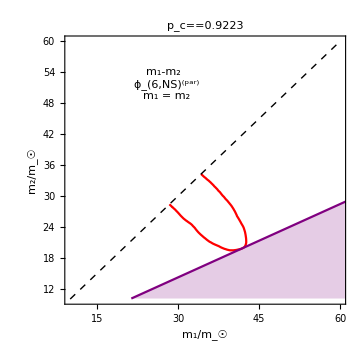

```mathematica
probability=prob;
(*probability=0.9220219417630785;*)

plots[p]=PlotInversion[p,probability,10,60,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### phi_7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_7"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 8}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.000538};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,8}

m1范围：{11.487,285.216}

m2范围：{4.45651,91.8959}

对称数据：原始 14982 + 镜像 14982

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.27868×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.27868×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.45651, 285.216} × {4.45651, 285.216}

等高线值：{0.000538}，共 2 条

第一条前3点：{{35.0901,34.2128},{35.1347,34.1607},{35.3595,33.9463}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.964957

可信水平百分比：96.4957%

==========================

dphi_7 预处理完成，红线包含概率 prob = 0.964957

```mathematica
p="dphi_7"; 
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.02155, 0.97845}

实际使用的 GR 概率区间上下界: {1112.45, 1130.89}

实际使用的 Param 概率区间上下界: {1129.34, 8354.33}

GR下界: 点数=250 | Y>0点数=250 | 平均误差=9.91349×10^-14

GR上界: 点数=250 | Y>0点数=250 | 平均误差=3.36513×10^-14

Param下界: 点数=250 | Y>0点数=250 | 平均误差=8.73115×10^-14

Param上界: 点数=250 | Y>0点数=250 | 平均误差=7223.43

{{10.2,8.36332},{10.4,8.52731},{10.6,8.6913},{10.8,8.85528},{11.,9.01927}}

{{10.2,10.2047},{10.4,10.3984},{10.6,10.6064},{10.8,10.8071},{11.,10.9922}}

chi1L取值：0.272612

chi2L取值：0.300481

=====================================================

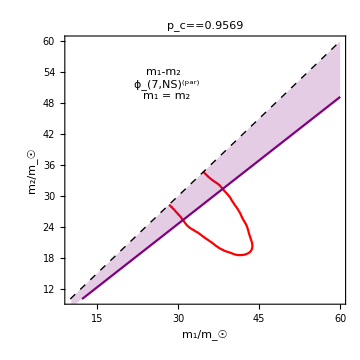

```mathematica
probability=prob;
probability=0.9569;
(*0.32*)
plots[p]=PlotInversion[p,probability,10,60,0.2,cm->True,cd->False,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},upStyle->Directive[Purple,Opacity[0]]]
```

## Intermediate

### beta_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0015};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 60315 + 镜像 60315

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.998414 and 3.80329×10^-6 for the integral and error estimates.

对称先验空间积分 = 0.998414（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.80933×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.0015}，共 2 条

第一条前3点：{{14.9752,15.975},{14.9736,15.9753},{14.834,16.1275}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.430459

可信水平百分比：43.0459%

==========================

dbeta_2 预处理完成，红线包含概率 prob = 0.430459

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
probability=prob;
probability=0.1028;
probability=0.1964;

PlotInversion[p,probability,3,40,0.2,cm->True,cd->True,cu->True,plotgr->True,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

====== [dbeta_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.4018, 0.5982}

实际使用的 GR 概率区间上下界: {-3.07591, -2.73963}

实际使用的 Param 概率区间上下界: {-4.31193, -3.1868}

GR下界: 点数=185 | Y>0点数=185 | 平均误差=1.10182×10^-15

GR上界: 点数=185 | Y>0点数=185 | 平均误差=1.16663×10^-15

Greater::nord: Invalid comparison with 0.669431+3.1292 ⅈ attempted.

Greater::nord: Invalid comparison with 0.712579+3.32449 ⅈ attempted.

Greater::nord: Invalid comparison with 0.754688+3.52001 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Param下界: 点数=185 | Y>0点数=0 | 平均误差=0.0285144

Param上界: 点数=185 | Y>0点数=6 | 平均误差=0.000187368

{{3.2,0.669431+3.1292 ⅈ},{3.4,0.712579+3.32449 ⅈ},{3.6,0.754688+3.52001 ⅈ},{3.8,0.79672+3.71554 ⅈ},{4.,0.838738+3.91108 ⅈ}}

{{3.2,3.2},{3.4,3.4},{3.6,3.6},{3.8,3.8},{4.,4.}}

chi1L取值：0.432612

chi2L取值：0.485378

=====================================================

-Graphics-

```mathematica
Quantile[samples[p][[7]],0.5+0.2056/2]
```

-3.10171

```mathematica
IMRPhenomDBeta[2,30,30,Median[samples[p][[3]]],Median[samples[p][[4]]]]
```

-3.21413

```mathematica
Median[samples[p][[4]]]
```

0.489687

```mathematica
Quantile[samples[p][[7]],0.5+0.5603/2/2]
IMRPhenomDBeta[2,74.33866621071876,43,Median[samples[p][[3]]],Median[samples[p][[4]]]]
```

-3.02386

-3.02386

```mathematica
p="dbeta_2"
Median[samples[p][[4]]]
```

dbeta_2

0.489687

### beta_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{20,40}, {1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.02035};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],1]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{20,40}

输入q范围：{1,3}

m1范围：{22.974,81.9069}

m2范围：{13.6512,45.9479}

对称数据：原始 18356 + 镜像 18356

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.92784×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.92784×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{13.6512, 81.9069} × {13.6512, 81.9069}

等高线值：{0.02035}，共 2 条

第一条前3点：{{32.1994,31.9863},{32.2014,31.9858},{32.2231,31.9794}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.0262264

可信水平百分比：2.62264%

==========================

dbeta_3 预处理完成，红线包含概率 prob = 0.0262264

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.487, 0.513}

实际使用的 GR 概率区间上下界: {-0.0000135733, -0.0000134121}

实际使用的 Param 概率区间上下界: {-0.0000134319, -0.000013169}

Greater::nord: Invalid comparison with 21.6923+19.247 ⅈ attempted.

Greater::nord: Invalid comparison with 22.4178+19.9359 ⅈ attempted.

Greater::nord: Invalid comparison with 23.1509+20.6164 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR下界: 点数=15 | Y>0点数=3 | 平均误差=4.35019×10^-8

GR上界: 点数=15 | Y>0点数=15 | 平均误差=2.25875×10^-21

Param下界: 点数=15 | Y>0点数=15 | 平均误差=1.58113×10^-21

Param上界: 点数=15 | Y>0点数=15 | 平均误差=1.12938×10^-21

{{26,27.2916},{27,28.3413},{28,29.391},{29,30.4406},{30,31.4903}}

{{26,76.7554},{27,79.7076},{28,82.6597},{29,85.6118},{30,88.564}}

chi1L取值：0.391925

chi2L取值：0.403678

=====================================================

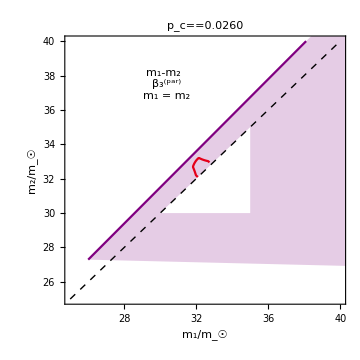

```mathematica
probability=prob;
(*probability=0.026;*)
probability=0.0260;
(*probability=0.0261;*)

(* 蓝色要对称一下 *)
PlotInversion[p,probability,25,40,1,cm->True,cd->False,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

## Merger-RingDown

### alpha_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,50}, {1, 3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.014223};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],1]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,50}

输入q范围：{1,3}

m1范围：{11.487,102.384}

m2范围：{6.82558,57.4349}

对称数据：原始 14828 + 镜像 14828

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 5.09221×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 5.09221×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{6.82558, 102.384} × {6.82558, 102.384}

等高线值：{0.014223}，共 2 条

第一条前3点：{{32.9417,33.2404},{32.8931,33.2744},{32.8344,33.3154}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.0958948

可信水平百分比：9.58948%

==========================

dalpha_2 预处理完成，红线包含概率 prob = 0.0958948

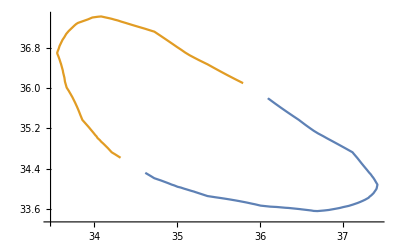

```mathematica
ListLinePlot[contourPoints[p]]
```

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
prob
```

0.0967669

====== [dalpha_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.452053, 0.547947}

实际使用的 GR 概率区间上下界: {-0.0677403, -0.0651011}

实际使用的 Param 概率区间上下界: {-0.065345, -0.0616832}

Greater::nord: Invalid comparison with 22.9055-12.3441 ⅈ attempted.

Greater::nord: Invalid comparison with 22.9225-12.3547 ⅈ attempted.

Greater::nord: Invalid comparison with 22.9397-12.365 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR下界: 点数=700 | Y>0点数=0 | 平均误差=0.000089218

GR上界: 点数=700 | Y>0点数=700 | 平均误差=3.69347×10^-17

Param下界: 点数=700 | Y>0点数=700 | 平均误差=3.0551×10^-17

Param上界: 点数=700 | Y>0点数=700 | 平均误差=2.99562×10^-17

{{26.02,28.8738},{26.04,28.8959},{26.06,28.9181},{26.08,28.9403},{26.1,28.9625}}

{{26.02,49.1864},{26.04,49.2242},{26.06,49.262},{26.08,49.2999},{26.1,49.3377}}

chi1L取值：0.333189

chi2L取值：0.355229

=====================================================

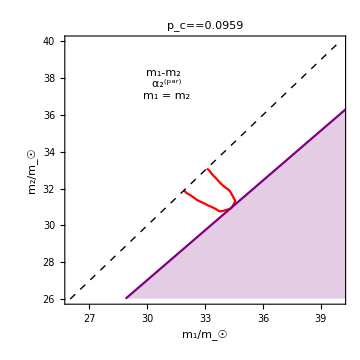

```mathematica
probability=prob;
(*probability=0.09676693194682148;*)
(*probability=0.09676693194682148;*)

plots[p]=PlotInversion[p,probability,26,40,0.02,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],1]}]
```

### alpha_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,60}, {1, 3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.013106};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],0.8]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.103216

可信水平百分比：10.3216%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.103216

输入Mc范围：{10,60}

输入q范围：{1,3}

m1范围：{11.487,122.86}

m2范围：{6.82558,68.9219}

对称数据：原始 17962 + 镜像 17962

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.47115×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.47115×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{6.82558, 122.86} × {6.82558, 122.86}

等高线值：{0.013106}，共 2 条

第一条前3点：{{32.3155,32.6782},{32.2861,32.7095},{32.2026,32.7867}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.103216

可信水平百分比：10.3216%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.103216

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
prob
```

0.101437

====== [dalpha_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.448392, 0.551608}

实际使用的 GR 概率区间上下界: {-24.7882, -22.4452}

实际使用的 Param 概率区间上下界: {-22.8231, -17.1401}

Greater::nord: Invalid comparison with 24.8308-7.77648 ⅈ attempted.

Greater::nord: Invalid comparison with 24.8483-7.78741 ⅈ attempted.

Greater::nord: Invalid comparison with 24.866-7.79787 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR下界: 点数=700 | Y>0点数=0 | 平均误差=0.19699

GR上界: 点数=700 | Y>0点数=700 | 平均误差=3.20556×10^-14

Param下界: 点数=700 | Y>0点数=700 | 平均误差=3.3294×10^-14

Param上界: 点数=700 | Y>0点数=700 | 平均误差=3.56692×10^-14

{{26.02,29.6978},{26.04,29.7206},{26.06,29.7434},{26.08,29.7663},{26.1,29.7891}}

{{26.02,48.5189},{26.04,48.5562},{26.06,48.5935},{26.08,48.6308},{26.1,48.6681}}

chi1L取值：0.306213

chi2L取值：0.385268

=====================================================

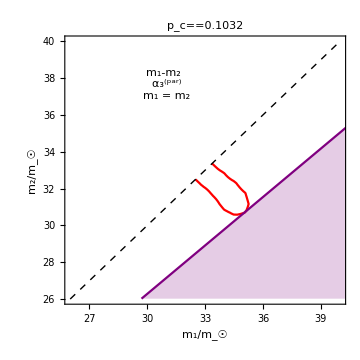

```mathematica
probability=prob;
(*probability=0.10143743087898953;*)

plots[p]=PlotInversion[p,probability,26,40,0.02,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### alpha_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{15,45}, {1, 5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.016693};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{15,45}

输入q范围：{1,5}

m1范围：{17.2305,122.583}

m2范围：{8.17221,51.6914}

对称数据：原始 18402 + 镜像 18402

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.44978×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.44977×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{8.17221, 122.583} × {8.17221, 122.583}

等高线值：{0.016693}，共 2 条

第一条前3点：{{33.7995,31.875},{33.8112,31.8682},{33.8955,31.8158}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.0364224

可信水平百分比：3.64224%

==========================

dalpha_4 预处理完成，红线包含概率 prob = 0.0364224

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
prob
```

0.04027

dalpha_4

====== [dalpha_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.481789, 0.518211}

实际使用的 GR 概率区间上下界: {0.266504, 0.266816}

实际使用的 Param 概率区间上下界: {0.260767, 0.267496}

GR下界: 点数=600 | Y>0点数=600 | 平均误差=5.61588×10^-17

GR上界: 点数=600 | Y>0点数=600 | 平均误差=4.73695×10^-17

Param下界: 点数=600 | Y>0点数=600 | 平均误差=5.34757×10^-17

Param上界: 点数=600 | Y>0点数=600 | 平均误差=5.4586×10^-17

{{28.02,39.2093},{28.04,39.2372},{28.06,39.2652},{28.08,39.2932},{28.1,39.3212}}

{{28.02,31.3611},{28.04,31.3834},{28.06,31.4058},{28.08,31.4282},{28.1,31.4506}}

chi1L取值：0.379054

chi2L取值：0.370003

=====================================================

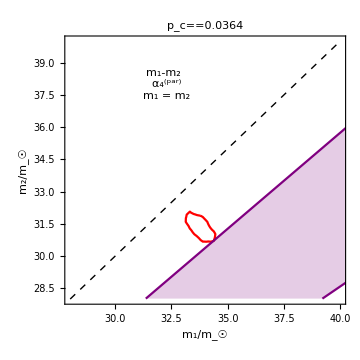

```mathematica
probability=prob;
p(*robability=0.04026996258853606;*)

plots[p]=PlotInversion[p,probability,28,40,0.02,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1}]
```

# Total plots

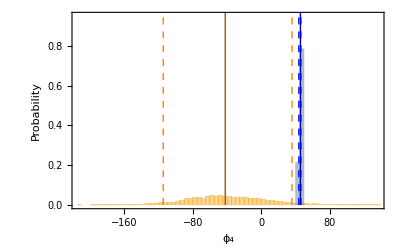

正在导出矢量图: plot_dphi_4_comp.pdf ...

正在导出矢量图: plot_dphi_7_comp.pdf ...

```mathematica
p="dphi_4"; 
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],Style["4",Italic]
,50
,Automatic
]
p="dphi_7"; 
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],Style["7",Italic]
,50
,Automatic
];
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\","comp"}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,"_comp.pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>"_comp.pdf"}],compPlots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[compPlots]}]
```

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>".pdf"}],plots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[plots]}]
```

正在导出矢量图: plot_dphi_5l.pdf ...

正在导出矢量图: plot_dphi_6.pdf ...

正在导出矢量图: plot_dphi_7.pdf ...

正在导出矢量图: plot_dalpha_2.pdf ...

正在导出矢量图: plot_dalpha_3.pdf ...

正在导出矢量图: plot_dalpha_4.pdf ...